# Training the spider-or-not classifier

This notebook contains the code used for training a neural network to classify images of arthropods into the categories “Spider” and “Non-spider”.

#### Notes on running this code:

The initialization cells (grey cells) are automatically run when accepting a prompt asking if you want all initialization cells run after running any cell in the notebook for the first time. The code in those cells prepare the training and validation sets. After those are run you can jump to the section “Use transfer learning to train the network” and follow the instructions there.

To ensure reproducibility, all code cells containing a function that uses randomness, the random number generator is re-set using a pre-generated random number as a seed.

The system OS and Mathematica version in which this code was run is

OperatingSystem: Unix
System: Linux x86 (64-bit)
Mathematica version: 13.1.0 for Linux x86 (64-bit) (June 16, 2022)

```mathematica
Column[{$OperatingSystem,$System,$Version}]
```

Unix
Linux x86 (64-bit)
13.1.0 for Linux x86 (64-bit) (June 16, 2022)

## Training images

These are in both the GitHub and figshare datasets in compressed format. You can uncompress them manually, or run the following code:

```mathematica
ExtractArchive[FileNameJoin[{dataDirectory,"TrainingImages.zip"}],FileNameJoin[{dataDirectory}],CreateIntermediateDirectories->True];
```

Check that the training images have the directories for Spider and NonSpider, and each one contains a list of image file names:

```mathematica
Length@FileNames["*",FileNameJoin[{dataDirectory,"TrainingImages","NonSpider"}]]
```

749

```mathematica
Length@FileNames["*",FileNameJoin[{dataDirectory,"TrainingImages","Spider"}]]
```

273

## Initialization

#### Images for training

imageDir should have three subdirectories,  “Spiders”, “NonSpiders” and “Mimics”. The images in “Spiders” and “NonSpiders” are going to be used for training, and the images in “Mimics” are used to explore how the trained network responds to mimics.

```mathematica
projectDir = DirectoryName@NotebookDirectory[];
imageDir = FileNameJoin[{projectDir,"Data","TrainingImages"}];
spiderFiles=FileNames["*",FileNameJoin[{imageDir,"Spider"}]];
nonspiderFiles=FileNames["*",FileNameJoin[{imageDir,"NonSpider"}]];
```

View the amount of images in each category

```mathematica
Length/@{spiderFiles,nonspiderFiles}
```

{273,749}

#### Assign categories to training data

```mathematica
randomSplit::usage = "randomSplit[list, point] pseudorandomly splits list into two smaller lists. The split is done at the position given by point.";
randomSplit[list_, point_]:=Module[{splitPosition,randomList},
	splitPosition=Floor[Length[list]*point];
	randomList=RandomSample[list];
	{randomList[[;;splitPosition]], randomList[[splitPosition+1;;]]}
]
```

Randomly assign images into a training and a validation set, where the training set contains 90% of the full data, and the validation set contains the remaining images.
Note that mimics are categorized as a NonSpider.

```mathematica
SeedRandom[547319];
(* Create lists in the form ImageFile->Category *)
spiderFilesClassified = Thread[Rule[File/@spiderFiles, "Spider"]];
nonspiderFilesClassified = Thread[Rule[File/@nonspiderFiles, "NonSpider"]];

(* Randomly split the spider and non-spider categories into the training and validation sets *)
{spiderTraining, spiderValidation} = randomSplit[spiderFilesClassified, .9];
{nonspiderTraining, nonspiderValidation} = randomSplit[nonspiderFilesClassified, .9];
(* Join the spider and non spider training and validation sets *)
trainingSet=Join[nonspiderTraining,spiderTraining];
validationSet=Join[nonspiderValidation,spiderValidation];
```

Check sizes of each training set

```mathematica
Length/@{trainingSet, validationSet}
```

{919,103}

## Use transfer learning to train the network

The neural network used here was obtained through the Wolfram neural net repository: https://resources.wolframcloud.com/NeuralNetRepository/resources/EfficientNet-Trained-on-ImageNet/

Take all but the last two layers of EfficientNet

```mathematica
slicedNet=Take[NetModel["EfficientNet Trained on ImageNet"],{1,-3}]
```

NetChain[<>]

Add two layers and a decoder which decodes into two categories, one for Spider and one for NonSpider

```mathematica
mimicNet=NetChain[<|"pretrainedNet"->slicedNet,"linearNew"->LinearLayer[],"softmax"->SoftmaxLayer[]|>,"Output"->NetDecoder[{"Class",{"Spider","NonSpider"}}]]
```

NetChain[<>]

Train the net. Use the commented code if there is a GPU available and you want to use it, although it won’t take much time without one. (It took around 10 minutes in an average laptop without GPU). Run the un-commented code to replicate the results shown in this notebook.

```mathematica
SeedRandom[680049];
(*
trainedNet=NetTrain[mimicNet,trainingSet,LearningRateMultipliers->{"linearNew"->1,_->0},TargetDevice->"GPU"]
*)
trainedMimicNet=NetTrain[mimicNet,trainingSet,LearningRateMultipliers->{"linearNew"->1,_->0}]
```

NetChain[<>]

Store the trained network in a .m file:

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"SpiderClassifier.m"}],trainedMimicNet]
```

Check accuracy of the network as the proportion of images classified accurately and visualize it in a ConfusionMatrixPlot:

```mathematica
netCMs=ClassifierMeasurements[trainedMimicNet,validationSet,ComputeUncertainty->True];
```

```mathematica
netCMs["Accuracy"]
```

0.990291

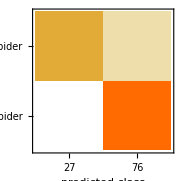

-Graphics-

```mathematica
netCMs["ConfusionMatrixPlot"]
```

Visualize the worst classified examples:

```mathematica
worstClassExFile=First@Cases[netCMs["WorstClassifiedExamples"],Rule[file_File,_]:>file];
```

```mathematica
worstClassEx=Import[worstClassExFile];
Thumbnail@worstClassEx
```

-Graphics-

```mathematica
trainedMimicNet[worstClassEx,"Probabilities"]
```

<|Spider→0.361847,NonSpider→0.638153|>

## Explore the features used by the trained network to identify spiders vs non-spiders:

Following https://www.wolfram.com/language/12/neural-network-framework/visualize-the-insides-of-a-neural-network.html, the following code can be used to produce images which the DCNN classifies as Spiders or NonSpiders with high confidence:

```mathematica
jitter[{dx_,dy_}][img_Image]:=ImagePad[img,{dx {1,-1},dy {1,-1}},"Periodic"];
imageMaximizeClass[image_Image,channel_,loopCount_]:=Module[
{featureNet,netDims,newImg,offset,imageList},
netDims=NetExtract[trainedMimicNet,{"Input","ImageSize"}];
newImg=ImageResize[image,netDims];
featureNet=NetAppend[NetTake[trainedMimicNet,"softmax"],"L2_norm"->{PartLayer[channel],ElementwiseLayer[x↦x^2],SummationLayer[]}];
imageList=Join[{image},
Table[
offset=RandomInteger[{-8,8},{2}];
newImg=ImageClip@ImageAdd[newImg,
jitter[-offset][Image[Normalize[featureNet[jitter[offset][newImg],NetPortGradient["Input"]],array↦8 Max@Abs@Flatten[array]],Interleaving->False]]
],
{n,loopCount}
]	
];
imageList
];
imageMaximizeClass[image:"Random",channel_,loopCount_]:=Module[
{randomImg,meanColor,netDims},
meanColor=NetExtract[trainedMimicNet,{"Input","MeanImage"}];
netDims=NetExtract[trainedMimicNet,{"Input","ImageSize"}];
randomImg=Nest[img↦ImageEffect[GaussianFilter[img,{6,2},Padding->"Periodic"],{"GaussianNoise",0.05}],ConstantImage[meanColor,netDims],4];
imageMaximizeClass[randomImg,channel,loopCount]
]
```

#### Creating a random image and modify it to look like a spider (to the network)

```mathematica
randomImageToSpider=imageMaximizeClass["Random",1,25];
```

```mathematica
randomImageToSpider[[-1]]//Thumbnail
```

-Graphics-

The first image (a randomly generated image) is classified as a non spider a relatively low confidence:

```mathematica
trainedMimicNet[First@randomImageToSpider,"Probabilities"]
```

<|Spider→0.187829,NonSpider→0.812171|>

While the last image, which has been modified, is now classified as a spider with a really high confidence:

```mathematica
trainedMimicNet[Last@randomImageToSpider,"Probabilities"]
```

<|Spider→1.,NonSpider→2.62394×10^-15|>

After 5 cycles the confidence is almost 1.

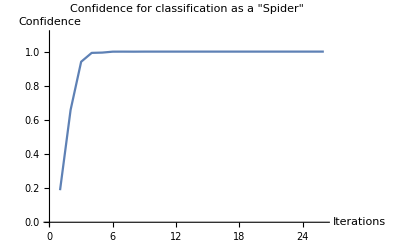

```mathematica
ListLinePlot[trainedMimicNet[randomImageToSpider,"Probabilities"][[All,"Spider"]],PlotLabel->"Confidence for classification as a \"Spider\"",AxesLabel->{"Iterations","Confidence"},PlotRange->{0,1.1}]
```

#### Creating a random image and modify it to look like a non-spider (to the network)

```mathematica
randomImageToNonSpider=imageMaximizeClass["Random",2,25];
```

```mathematica
randomImageToNonSpider[[-1]]//Thumbnail
```

-Graphics-

```mathematica
trainedMimicNet[Last@randomImageToNonSpider,"Probabilities"]
```

<|Spider→9.0066×10^-11,NonSpider→1.|>